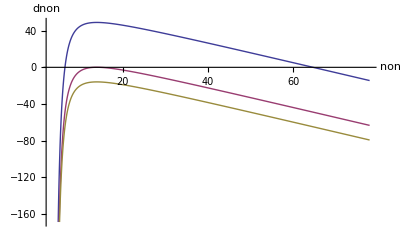

```mathematica
dnon1 = -non*koff0*Exp[F/(non*F0)]+kon*(ntot1-non);
dnon2 = -non*koff0*Exp[F/(non*F0)]+kon*(ntot2-non);
dnon3 = -non*koff0*Exp[F/(non*F0)]+kon*(ntot3-non);
params ={koff0 -> 0.1 , F0 -> 2 , kon -> 1, F -> 60, ntot1-> 75, ntot2-> 26, ntot3->10};
Needs["PlotLegends`"];

Plot [{dnon1/.params , dnon2/.params, dnon3/.params} ,{non ,3,78},AxesLabel-> {"non", "dnon"},  PlotLegend->{"ntot=75" , "ntot=26" , "ntot=10"}, LegendPosition-> {1.2,-0.5}]
```